# A model with a single firm

## General assumptions

All distributions are continuous.

Agents make independent choices.

## A model of an agent population

We need to have two random variables. The first random variable describes a distribution of reservation prices. Let’s call it R. For example, we can have a Gamma distribution. The following is an example of a particular parameter choice that we can have if we want to reflect that in the population there is some common reservation price, but we do have some variation.

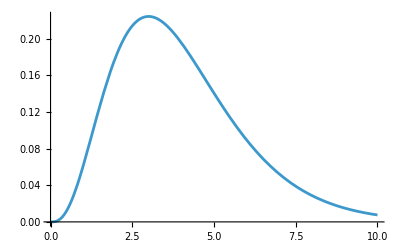

```mathematica
ℛ=GammaDistribution[4,1];
Plot[PDF[ℛ,x],{x, 0, 10},PlotRange->All]
```

The other type of distribution is about the particular style preference of an agent. Let’s call it S. We want the values of this distribution to fall in the interval [0,1]. For this, we can use the uniform distribution or a Beta distribution. The following are examples of two types of distributions. The choice of the beta distribution is smart because it contains the uniform distribution, but also it may reflect the fact that there is like a common value for the style choice with some variation.

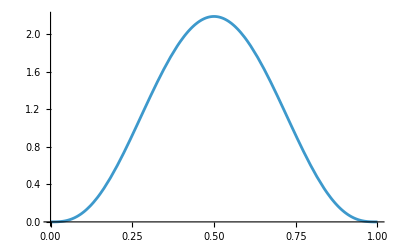

```mathematica
𝒮=BetaDistribution[4,4];
Plot[PDF[𝒮,x],{x, 0, 1},PlotRange->All]
```

The first step for the agent is to look at the price of the good. The utility of the agent from facing the good with price p and style o is the following

u(r, s, p, o)=-α·p/r-β·(s-o)^2

where r is a realization of the random variable R, s is a realization of the random variable S, p is the offered price of a good (assumed non-negative) with the style o. We can view u as the random variable

U=-α·p/R-β·(S-o)^2

The probability that a consumer buys the good is given by the folowing formula

ℙ(buy)=(exp(u))/(1+exp(u))

and the probability of not buy is given by the following formula

ℙ(not buy)=1/(1+exp(u))=1-(exp(u))/(1+exp(u))

We can view the probability of buying as a random variable that reads

ℙ(buy)=(exp(U))/(1+exp(U))=(exp(-α·p/R-β·(S-o)^2))/(1+exp(-α·p/R-β·(S-o)^2))

Let’s have an example.

```mathematica
ℛ=GammaDistribution[4,1];
𝒮=𝒮=BetaDistribution[4,4];
α=-1;
β=-1;
p=1;
o=1/2;
```

```mathematica
𝒰=TransformedDistribution[Exp[(-α p/r-β (s-o)^2)]/(1+Exp[(-α p/r-β (s-o)^2)]),{r\[Distributed]ℛ,s\[Distributed]𝒮}]
```

TransformedDistribution[(ⅇ^(1/x1+(-1/2+x2)^2))/(1+ⅇ^(1/x1+(-1/2+x2)^2)),{x1\[Distributed]GammaDistribution[4,1],x2\[Distributed]BetaDistribution[4,4]}]

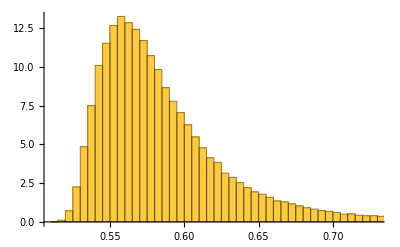

```mathematica
Histogram[RandomVariate[𝒰,10^5],"Scott","PDF"]
```

## A model of a firm

What is the expected profit of a single firm offering a good at price p and with the style o? The expected profit of a firm is then the following

𝔼(expected profit)=p·demand-c(demand)=p·N·ℙ(buy)-c(N·ℙ(buy))

Note that ℙ(buy) depends on p and o, which are controlled by a firm. Thus, a firm may adjust these parameters to maximize the expected profit. We assume that the style of the good o is fixed, which makes the price p the only maximization parameter.

First order condtions read

ⅆ/ⅆp(𝔼(expected profit))=ⅆ/ⅆp(p·𝔼[demand]-c(𝔼[demand]))=ⅆ/ⅆp(p·𝔼[demand])-ⅆ/ⅆp(c(𝔼[demand]))=𝔼[demand]+p·(ⅆ 𝔼[demand])/ⅆp-MC(𝔼[demand])·(ⅆ 𝔼[demand])/ⅆp=0

Let’s have an exmaple.

```mathematica
ℛ=GammaDistribution[4,1];
𝒮=𝒮=BetaDistribution[4,4];
α=-1;
β=-1;
Remove[p];
o=1/2;
n=100;
c=1;
```

```mathematica
𝒰=TransformedDistribution[Exp[(-α p/r-β (s-o)^2)]/(1+Exp[(-α p/r-β (s-o)^2)]),{r\[Distributed]ℛ,s\[Distributed]𝒮}]
```

TransformedDistribution[(ⅇ^((-1/2+x2)^2+p/x1))/(1+ⅇ^((-1/2+x2)^2+p/x1)),{x1\[Distributed]GammaDistribution[4,1],x2\[Distributed]BetaDistribution[4,4]}]

```mathematica
𝒫=TransformedDistribution[p n u-c (n u)^2,u\[Distributed]𝒰]
```

TransformedDistribution[100 p u-10000 u^2,u\[Distributed]TransformedDistribution[(ⅇ^((-1/2+x2)^2+p/x1))/(1+ⅇ^((-1/2+x2)^2+p/x1)),{x1\[Distributed]GammaDistribution[4,1],x2\[Distributed]BetaDistribution[4,4]}]]

```mathematica
expecteProfit[pp_]:=Mean[RandomVariate[Evaluate[𝒫/.p->pp],10^3]]
```

General::munfl: 1/(6.1874×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.50136×10^308) is too small to represent as a normalized machine number; precision may be lost.

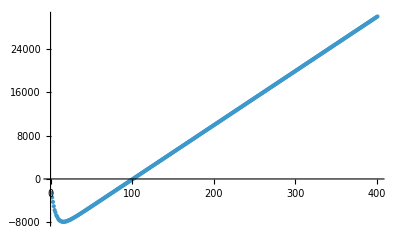

```mathematica
ListPlot[
Table[expecteProfit[p],{p,0,400}]
]
```

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michael/Documents/git_projects/mgr/bojarin_bogdan/MasterThesis75184SGH/wolfram